# CRMSD and D

## Ka=0

## data loading

```mathematica
p0s={3.85,3.825,3.80,3.775,3.75};
```

```mathematica
temperatures={{0.039 ,0.016, 0.01 ,0.005 ,0.00385, 0.0025 ,0.002, 0.001 ,0.0005 ,0.00033 ,0.00025, 0.00014, 0.000091,0.000077,0.000054, 0.000045, 0.000036},{0.063 ,0.039, 0.03105, 0.016 ,0.01, 0.008, 0.0063, 0.005 ,0.00385, 0.0031, 0.0025, 0.002, 0.0015, 0.001, 0.00067 ,0.0005},{0.063 ,0.039 ,0.03105, 0.025, 0.016 ,0.01 ,0.008 ,0.0063, 0.005, 0.00385, 0.0031, 0.0028 ,0.0025 ,0.0022},{0.03105, 0.025 ,0.02 ,0.016 ,0.012, 0.01, 0.009 ,0.008 ,0.0075, 0.007 ,0.0063, 0.0056 ,0.0054},{0.063, 0.039, 0.03105, 0.025 ,0.02, 0.016, 0.014,0.012 ,0.011, 0.01, 0.0093}};
 records={{10, 11, 12 ,13, 14 ,15 ,16, 17 ,18 ,19},{10, 11, 12 ,13, 14 ,15 ,16, 17 ,18 ,19},{10, 11, 12 ,13, 14 ,15 ,16, 17 ,18 ,19},{10, 11, 12 ,13, 14 ,15 ,16, 17 ,18 ,19},{10, 11, 12 ,13, 14 ,15 ,16, 17 ,18 ,19}};
tauEstimate={{2, 4,10, 20, 40,60, 80, 200, 500, 800, 1400, 2500, 4200,5000, 6000, 8500, 9500},{1, 2, 4 ,9 ,15,25, 40 ,60, 80, 120,200 ,300 ,1000 ,1500, 5000,10000},{1, 3, 4 ,8 ,15,40 ,70 ,150 ,250, 600 ,2000, 2500 ,4500, 9500},{2, 10,20 ,30, 80 ,100 ,400 ,500 ,2500 ,2500, 3000 ,7000, 10000},{4 ,5 ,7 ,10 ,30 ,70, 150 ,700,1400, 4000 ,9500}};
```

```mathematica
sigmaXXsigmaYYs=Table[Table[DeleteCases[Table[Import[dataNameStringNumber[{"/home/chengling/Research/Project/Cell/glassyDynamics/N4096/tauAlphaData/p","/sigmaXXsigmaYY_perimeter_N4096_p","_T","_",".nc"},{p0s[[p]],p0s[[p]],temperatures[[p,T]],records[[p,i]]},{3,3,8,0}],"Data"],{i,Length[records[[p]]]}],$Failed],{T,Length[temperatures[[p]]]}],{p,Length[p0s]}];
```

Import::format: Cannot import data as Data.

General::stop: Further output of Import::format will be suppressed during this calculation.

```mathematica
Normal[sigmaXXsigmaYYs[[1,1,1,1]]]
```

{0.238835,0.231717,0.234327,0.225196,0.233277,0.234572,0.227311,0.231401,0.230818,0.230305,0.230275}

```mathematica
SigmaXX=Table[Table[Flatten[Table[DeleteCases[Table[sigmaXXsigmaYYs[[p,T,i,1,rec]],{i,Length[sigmaXXsigmaYYs[[p,T]]]}],_Missing|_Part],{rec,Max[Table[Length[sigmaXXsigmaYYs[[p,T,i,1]]],{i,Length[sigmaXXsigmaYYs[[p,T]]]}]]}]],{T,Length[temperatures[[p]]]}],{p,Length[p0s]}];
```

Part::partw: Part 11 of … does not exist.

Part::partw: Part 9 of … does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

```mathematica
SigmaYY=Table[Table[Flatten[Table[DeleteCases[Table[sigmaXXsigmaYYs[[p,T,i,2,rec]],{i,Length[sigmaXXsigmaYYs[[p,T]]]}],_Missing|_Part],{rec,Max[Table[Length[sigmaXXsigmaYYs[[p,T,i,1]]],{i,Length[sigmaXXsigmaYYs[[p,T]]]}]]}]],{T,Length[temperatures[[p]]]}],{p,Length[p0s]}];
```

Part::partw: Part 11 of … does not exist.

Part::partw: Part 9 of … does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

```mathematica
meanSigma=Table[Table[Mean[Table[Mean[{SigmaXX[[p,T,rec]],SigmaYY[[p,T,rec]]}],{rec,Length[SigmaXX[[p,T]]]}]],{T,Length[temperatures[[p]]]}],{p,Length[p0s]}];
```

## Plots and fitting

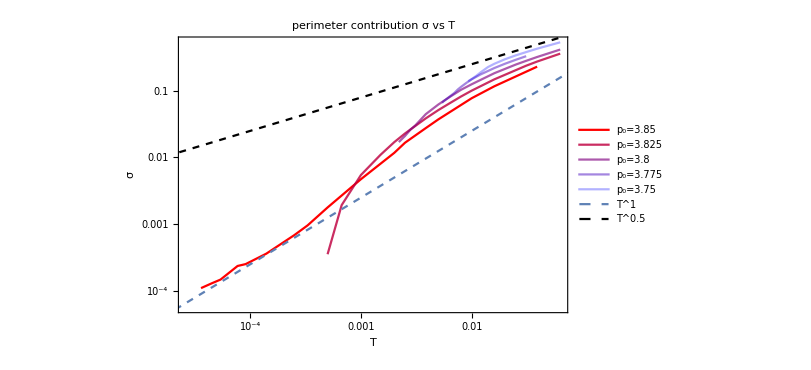

```mathematica
perPlot=Show[ListLogLogPlot[Table[Table[{temperatures[[p,T]],meanSigma[[p,T]]},{T,Length[temperatures[[p]]]}],{p,Length[p0s]}],PlotLegends->Table["p_0="<>ToString[p0s[[p]]],{p,Length[p0s]}],PlotStyle->redBluePlotConfig[Length[p0s]],FrameLabel->{"T","σ"},ImageSize->600,PlotLabel->"perimeter contribution σ vs T",Joined->True],LogLogPlot[2.5 x^1,{x,0.00001,0.1},PlotStyle->Dashed,PlotLegends->{"T^1"}],LogLogPlot[2.5 x^0.5,{x,0.00001,0.1},PlotStyle->{Dashed,Black},PlotLegends->{"T^0.5"}]]
```

```mathematica
Export["/home/chengling/Research/updates/04112024/perimeterSigma.jpeg",perPlot,ImageResolution->600]
```

/home/chengling/Research/updates/04112024/perimeterSigma.jpeg

## Ka=1.0

## data loading

```mathematica
p0s={3.85,3.825,3.80,3.775,3.75};
```

```mathematica
temperatures={{0.039 ,0.016, 0.01 ,0.005 ,0.00385, 0.0025 ,0.002, 0.001 ,0.0005 ,0.00033 ,0.00025, 0.00014, 0.000091,0.000077,0.000054, 0.000045, 0.000036},{0.063 ,0.039, 0.03105, 0.016 ,0.01, 0.008, 0.0063, 0.005 ,0.00385, 0.0031, 0.0025, 0.002, 0.0015, 0.001, 0.00067 ,0.0005},{0.063 ,0.039 ,0.03105, 0.025, 0.016 ,0.01 ,0.008 ,0.0063, 0.005, 0.00385, 0.0031, 0.0028 ,0.0025 ,0.0022},{0.03105, 0.025 ,0.02 ,0.016 ,0.012, 0.01, 0.009 ,0.008 ,0.0075, 0.007 ,0.0063, 0.0056 ,0.0054},{0.063, 0.039, 0.03105, 0.025 ,0.02, 0.016, 0.014,0.012 ,0.011, 0.01, 0.0093}};
 records={{10, 11, 12 ,13, 14 ,15 ,16, 17 ,18 ,19},{10, 11, 12 ,13, 14 ,15 ,16, 17 ,18 ,19},{10, 11, 12 ,13, 14 ,15 ,16, 17 ,18 ,19},{10, 11, 12 ,13, 14 ,15 ,16, 17 ,18 ,19},{10, 11, 12 ,13, 14 ,15 ,16, 17 ,18 ,19}};
tauEstimate={{2, 4,10, 20, 40,60, 80, 200, 500, 800, 1400, 2500, 4200,5000, 6000, 8500, 9500},{1, 2, 4 ,9 ,15,25, 40 ,60, 80, 120,200 ,300 ,1000 ,1500, 5000,10000},{1, 3, 4 ,8 ,15,40 ,70 ,150 ,250, 600 ,2000, 2500 ,4500, 9500},{2, 10,20 ,30, 80 ,100 ,400 ,500 ,2500 ,2500, 3000 ,7000, 10000},{4 ,5 ,7 ,10 ,30 ,70, 150 ,700,1400, 4000 ,9500}};
```

```mathematica
sigmaXXsigmaYYs=Table[Table[DeleteCases[Table[Import[dataNameStringNumber[{"/home/chengling/Research/Project/Cell/glassyDynamics/N4096/tauAlphaData/p","/sigmaXXsigmaYY_N4096_p","_T","_",".nc"},{p0s[[p]],p0s[[p]],temperatures[[p,T]],records[[p,i]]},{3,3,8,0}],"Data"],{i,Length[records[[p]]]}],$Failed],{T,Length[temperatures[[p]]]}],{p,Length[p0s]}];
```

Import::format: Cannot import data as Data.

General::stop: Further output of Import::format will be suppressed during this calculation.

```mathematica
sigmaXXsigmaYYs[[1,17]]
```

{<|/firstValue→NumericArray[…],/secondValue→NumericArray[…]|>,<|/firstValue→NumericArray[…],/secondValue→NumericArray[…]|>,<|/firstValue→NumericArray[…],/secondValue→NumericArray[…]|>,<|/firstValue→NumericArray[…],/secondValue→NumericArray[…]|>,<|/firstValue→NumericArray[…],/secondValue→NumericArray[…]|>,<|/firstValue→NumericArray[…],/secondValue→NumericArray[…]|>,<|/firstValue→NumericArray[…],/secondValue→NumericArray[…]|>,<|/firstValue→NumericArray[…],/secondValue→NumericArray[…]|>,<|/firstValue→NumericArray[…],/secondValue→NumericArray[…]|>,<|/firstValue→NumericArray[…],/secondValue→NumericArray[…]|>}

```mathematica
Normal[sigmaXXsigmaYYs[[1,1,1,1]]]
```

{0.251468,0.244393,0.247302,0.238019,0.246261,0.247319,0.239919,0.244294,0.243343,0.242202,0.242348}

```mathematica
Flatten[{{{1,2},2,{{2,1}}}}]
```

{1,2,2,2,1}

```mathematica
SigmaXX=Table[Table[Flatten[Table[DeleteCases[Table[sigmaXXsigmaYYs[[p,T,i,1,rec]],{i,Length[sigmaXXsigmaYYs[[p,T]]]}],_Missing|_Part],{rec,Max[Table[Length[sigmaXXsigmaYYs[[p,T,i,1]]],{i,Length[sigmaXXsigmaYYs[[p,T]]]}]]}]],{T,Length[temperatures[[p]]]}],{p,Length[p0s]}];
```

Part::partw: Part 11 of … does not exist.

Part::partw: Part 9 of … does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

```mathematica
SigmaYY=Table[Table[Flatten[Table[DeleteCases[Table[sigmaXXsigmaYYs[[p,T,i,2,rec]],{i,Length[sigmaXXsigmaYYs[[p,T]]]}],_Missing|_Part],{rec,Max[Table[Length[sigmaXXsigmaYYs[[p,T,i,1]]],{i,Length[sigmaXXsigmaYYs[[p,T]]]}]]}]],{T,Length[temperatures[[p]]]}],{p,Length[p0s]}];
```

Part::partw: Part 11 of … does not exist.

Part::partw: Part 9 of … does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

```mathematica
meanSigma=Table[Table[Mean[Table[Mean[{SigmaXX[[p,T,rec]],SigmaYY[[p,T,rec]]}],{rec,Length[SigmaXX[[p,T]]]}]],{T,Length[temperatures[[p]]]}],{p,Length[p0s]}];
```

```mathematica
sigmaXXsigmaYYs[[1,17,1,1,1]]
sigmaXXsigmaYYs[[1,17,1,2,1]]
```

0.00034151

0.000490287

```mathematica
SigmaXX[[1,17]]
```

{0.00034151,-0.0000306889,0.000226024,-0.0000529803,0.0000445695,0.000144326,0.0000605404,-0.000136053,0.000264118,0.000155824,0.000206331,0.000239464,-0.0000222679,0.000151971,0.00034372,-0.0000806843,-0.000257677,0.000525036,-0.00011122,0.0004386,-0.000236799,0.000247389,0.0000345137,-0.000265242,0.000104263,-0.000424779,0.000213987,0.0000456063,0.000440075,-0.000107169,-5.4046×10^-6,-0.000106859,-0.000186738,0.000107077,0.000125252,0.000135802,-0.00016013,0.000241207,0.00028117,0.00025458,0.000331732,0.0000905649,0.000511651,0.000258194,0.000208601,0.000487919,0.0000819535,0.000361796,0.0000436405,-0.000105323,0.000503352,0.000324311,0.000235671,0.000137833,-0.00009587,0.000155439,0.000289947,0.0000480231,0.000707218,0.0000121716,0.000294954,-0.000260192,0.000242766,0.000209986,-0.000242962,0.000863949,0.0000992149,0.0000751219,-0.000146773,0.000757332,0.000155014,0.000415628,0.000199664,0.000157827,0.000646973,0.000307869,-0.0000871545,0.000413788,-0.0000601921,-0.000348185,0.000636164,0.000209498,0.000439249,0.000108741,0.000310632,0.0000187684,-0.0002041,0.000284014,0.000847261,-0.000246344,0.000448416,0.0000183523,0.000181876,-0.0000515647,0.000172957,0.0000535783,0.0000403683,-0.0000128003,0.00033388,0.0000963884,0.000618478,0.000321474,-0.000234194,0.0000738078,-0.0000429686,0.0000599572,0.000323517}

```mathematica
SigmaYY[[1,17]]
```

{0.000490287,-0.000150299,0.000227721,-0.0000857984,0.000106458,0.000143464,-0.000055151,-0.000287818,0.000334568,0.0000429744,0.000195971,0.000316291,-0.0000287005,0.000101091,0.000310142,-0.0000563737,-0.000125295,0.00048296,-0.0000568091,0.000459313,-0.000321841,0.000116006,-0.0000623558,-0.000219868,0.000218483,-0.000413689,0.000373234,-0.0000122117,0.000416942,-0.0000714372,-0.0000395299,-0.0000524894,-0.0000948705,0.000100175,0.000132794,0.00019177,-0.000243016,0.000174233,0.000209995,0.000142242,0.000336618,0.000283829,0.00052076,0.000311212,0.00012781,0.000499053,0.000231877,0.000257643,0.0000216973,-0.000135305,0.000565442,0.000257793,0.000271245,0.000162166,-0.000156738,0.0000870258,0.000139536,0.000120032,0.000694685,-0.0000966274,0.000273003,-0.000145863,0.000225713,0.000185764,-0.000337247,0.000804144,-0.0000751897,0.000128073,-0.000053118,0.00081975,0.000231921,0.000490621,0.000206633,0.000120297,0.000493854,0.000423451,-0.000165344,0.000254951,-0.0000183712,-0.000397375,0.000591319,0.000119598,0.000363667,0.0000968619,0.000442088,-0.0000250449,-0.000285534,0.0000853742,0.000842766,-0.000241639,0.000345436,-0.000127302,0.000193776,-0.0000189266,-0.0000814322,0.0000423852,0.0000394816,0.000117299,0.000381391,0.00012432,0.000443487,0.000250702,-0.000212619,0.000183212,0.0000446561,-0.0000920646,0.000319835}

```mathematica
meanSigma
```

{{0.242348,0.122707,0.0815166,0.0397331,0.029611,0.018123,0.0129915,0.00546576,0.00219964,0.00125039,0.000910915,0.000493852,0.000339692,0.000310728,0.000200275,0.000173946,0.000145305},{0.378488,0.286368,0.247591,0.153941,0.104385,0.0852079,0.0674446,0.053609,0.0404255,0.0313115,0.0242639,0.0181281,0.0118575,0.00613485,0.00242185,0.00073791},{0.432577,0.332582,0.290842,0.255044,0.18873,0.128868,0.106265,0.0827065,0.0642734,0.0462353,0.031619,0.0273407,0.0221111,0.0179848},{0.33936,0.299126,0.260638,0.224099,0.179451,0.151713,0.134984,0.116724,0.106992,0.0954473,0.0834069,0.0716581,0.0676671},{0.550011,0.438535,0.389293,0.346652,0.303009,0.258264,0.230281,0.191235,0.17035,0.152504,0.141546}}

## Plots and fitting

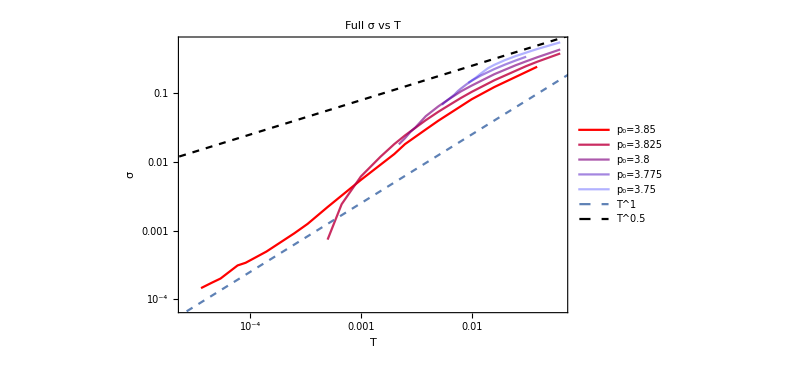

```mathematica
sigma=Show[ListLogLogPlot[Table[Table[{temperatures[[p,T]],meanSigma[[p,T]]},{T,Length[temperatures[[p]]]}],{p,Length[p0s]}],PlotLegends->Table["p_0="<>ToString[p0s[[p]]],{p,Length[p0s]}],PlotStyle->redBluePlotConfig[Length[p0s]],FrameLabel->{"T","σ"},ImageSize->600,PlotLabel->"Full σ vs T",Joined->True],LogLogPlot[2.5 x^1,{x,0.00001,0.1},PlotStyle->Dashed,PlotLegends->{"T^1"}],LogLogPlot[2.5 x^0.5,{x,0.00001,0.1},PlotStyle->{Dashed,Black},PlotLegends->{"T^0.5"}]]
```

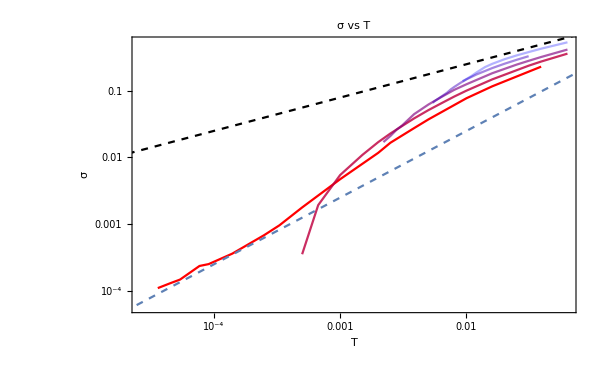

-Graphics-

```mathematica
Export["/home/chengling/Research/updates/04112024/fullSigma.jpeg",sigma,ImageResolution->600]
```

/home/chengling/Research/updates/04112024/fullSigma.jpeg

```mathematica
{}
```

{}